## Varying Energy

## Varying V_0

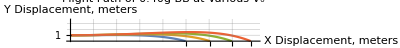

```mathematica
raw1=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/speed/250.csv"];
raw2=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/speed/300.csv"];
raw3=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/speed/350.csv"];
raw4=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/speed/400.csv"];
distMax=raw4[[-1,1]];
cut=0.97;
aspect=22;
maxes=Round[{raw1[[-1,1]],raw2[[-1,1]],raw3[[-1,1]],raw4[[-1,1]]},0.1];
ListLinePlot[{raw1,raw2,raw3,raw4},PlotRange->{{0,distMax/cut},{0,distMax/aspect/cut}},ImageSize->Full,AspectRatio->1/aspect,GridLines->{{10,20,30,40,50,60,70},{1,2,3,4,5}},PlotLabel->"Flight Path of 0.40g BB at Various V_0",AxesLabel->{"X Displacement, meters","Y Displacement, meters"},Ticks->{maxes, {1,3,5}},PlotLegends->Placed[{"250 FPS","300 FPS","350 FPS","400 FPS"},Below]]
```

#### Distance Difference

```mathematica
raw4[[-1,1]]-raw1[[-1,1]]
```

28.2039

## Varying Mass

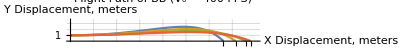

```mathematica
raw1=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/mass/25.csv"];
raw2=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/mass/30.csv"];
raw3=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/mass/36.csv"];
raw4=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/mass/40.csv"];
distMax=raw4[[-1,1]];
cut=0.97;first=0;aspect=22;
maxes=Round[{raw1[[-1,1]],raw2[[-1,1]],raw3[[-1,1]],raw4[[-1,1]]},0.1];
ListLinePlot[{raw1,raw2,raw3,raw4},PlotRange->{{first,distMax/cut},{first,distMax/aspect/cut}},ImageSize->Full,AspectRatio->1/aspect,GridLines->{{10,20,30,40,50,60,70},{1,2,3,4,5}},Ticks->{maxes, {1,3,5}},
PlotLabel->"Flight Path of BB (V_0 = 400 FPS)",
AxesLabel->{"X Displacement, meters","Y Displacement, meters"},
PlotLegends->Placed[{"0.25g","0.30g","0.36g","0.40g"},Below]
]
```

#### Distance Difference

```mathematica
raw4[[-1,1]]-raw1[[-1,1]]
```

11.7794

## Varying Hop

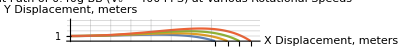

```mathematica
raw1=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/hop/175.csv"];
raw2=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/hop/200.csv"];
raw3=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/hop/225.csv"];
raw4=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/hop/250.csv"];
distMax=raw4[[-1,1]];
cut=0.97;first=0;aspect=22;
maxes=Round[{raw1[[-1,1]],raw2[[-1,1]],raw3[[-1,1]],raw4[[-1,1]]},0.1];
ListLinePlot[{raw1,raw2,raw3,raw4},PlotRange->{{first,distMax/cut},{first,distMax/aspect/cut}},ImageSize->Full,AspectRatio->1/aspect,GridLines->{{10,20,30,40,50,60,70},{1,2,3,4,5}},Ticks->{maxes, {1,3,5}},
PlotLabel->"Flight Path of 0.40g BB (V_0 = 400 FPS) at Various Rotational Speeds",
AxesLabel->{"X Displacement, meters","Y Displacement, meters"},
PlotLegends->Placed[{"175","200","225","250"},Below]
]
```

#### Distance Difference

```mathematica
raw4[[-1,1]]-raw1[[-1,1]]
```

17.6794

## Time Intersections

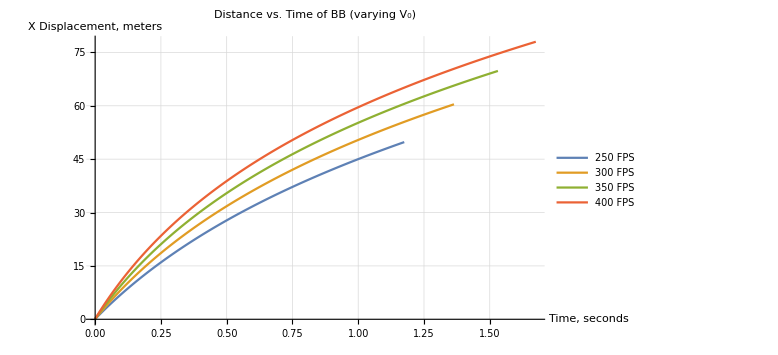

```mathematica
raw1=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/time/xt_250.csv"];
raw2=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/time/xt_300.csv"];
raw3=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/time/xt_350.csv"];
raw4=Import["/Users/leonard22/Desktop/CS/JS/AirsoftFlightPath/graphing/time/xt_400.csv"];
distMax=raw4[[-1,1]];
cut=1;first=0;aspect=2;
maxes=Round[{raw1[[-1,1]],raw2[[-1,1]],raw3[[-1,1]],raw4[[-1,1]]},0.1];
ListLinePlot[{raw1,raw2,raw3,raw4},PlotRange->Automatic,ImageSize->Large,GridLines->Automatic,
PlotLabel->"Distance vs. Time of BB (varying V_0)",
AxesLabel->{"Time, seconds","X Displacement, meters"},
PlotLegends->Placed[{"250 FPS","300 FPS","350 FPS","400 FPS"},Below]
]
```

#### Distance Difference

```mathematica
raw4[[-1,1]]-raw1[[-1,1]]
```

0.5